平均场理论求解2d Ising Model的m-kT图——六边形

1

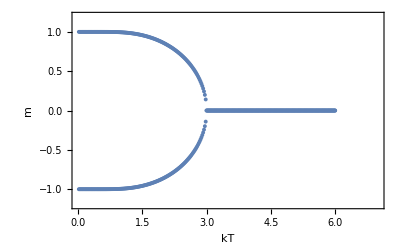

```mathematica
Clear["Global`*"]
J=1;
h = 0;
mm = Table[0,{i,300}];
jj = 1;
T= Table[i*0.02,{i,300}];
For[i0=1,i0≤300, i0 = i0 + 1,
β = 1/T[[i0]];
m1 = 0.0001;
m2 = 4;
k1= (m-Tanh[β*(3*J*m-h)])/.m->m1；
k2= (m-Tanh[β*(3*J*m-h)])/.m->m2；
If[k1*k2<0,
Do[
g1= (m-Tanh[β*(3*J*m-h)])/.m->m1;
m3 = (m1+m2)/2;
g2 =(m-Tanh[β*(3*J*m-h)])/.m->m3;
If[g1*g2<0,m2=m3,m1 =m3];
If[Abs[m1-m2]<0.001,Break],
{n,100000}];
mm[[jj]]=(m1+m2)/2;
jj =jj+1;
]
]
w=1

m1=-mm;
Show[ListPlot[Table[{T[[i]], mm[[i]]},{i,1,300}],PlotStyle->{PointSize[0.007]}],ListPlot[Table[{T[[j]], m1[[j]]},{j,1,300}],PlotStyle->{PointSize[0.007]}],PlotRange->{{0,7},{-1.2,1.2}},FrameLabel->{"kT","m"},Frame->True]
```